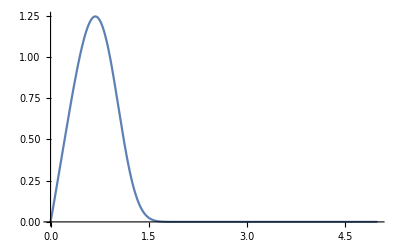

```mathematica
Plot[4*π*A*(x/b)^(a-3)*Exp[-(x/b)^c]*x^2/.{A->0.19956961662444025,a->2.02830461311898,b->0.968941823732608,c->3.6697132474259857},{x,0,5}]
```

```mathematica
Solve[D[4*π*A*(x/b)^(a-1)*Exp[-(x/b)^c],x]==0,x]
```

{{x→2^(-2/c) A^(-1/c) b^(1-1/c) c^(-1/c) π^(-1/c) (-4 A b π+4 a A b π)^(1/c)}}

```mathematica
FullSimplify[%]
```

{{x→A^(-1/c) b^(1-1/c) ((-1+a) A b)^(1/c) c^(-1/c)}}

```mathematica
{{x->A^(-1/c) b^(1-1/c) ((-1+a) A b)^(1/c) c^(-1/c)}}/.{A->0.19956961662444025,a->2.02830461311898,b->0.968941823732608,c->3.6697132474259857}
```

{{x→0.685075}}

```mathematica
4*π*A*(x/b)^(a-1)*Exp[-(x/b)^c]/.{A->0.19956961662444025,a->2.02830461311898,b->0.968941823732608,c->3.6697132474259857,x->0.6850750647269176}
```

1.32675